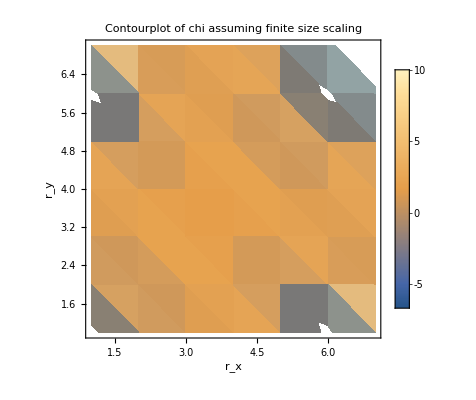

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
(****************************************)
Clear[data,datac,rx,ry,rho];
data=Import["result.dat","Table"];
rx=data[[;;,1]];
ry=data[[;;,2]];
rho=data[[;;,3]];
datac=Transpose[{rx,ry,rho}];
rhoplot=ListDensityPlot[datac,Axes->True,InterpolationOrder->6,FrameLabel->{"r_x","r_y"},PlotLabel->"Contourplot of chi assuming finite size scaling",PlotLegends->Automatic]
(*******************)
ListContourPlot[datac,Axes->True,InterpolationOrder->3,FrameLabel->{"r_x","r_y"},PlotLabel->"Contourplot of density fluctuation",ColorFunction->"Pastel",PlotLegends->Automatic];
ListPointPlot3D[{datac}];
ListPlot3D[{datac}]
(*Export["rhoplot.jpg",chiplot]*)
```